```mathematica
Remove["Global`*"]
```

```mathematica
h = {{0,ϵ*/2,0},{ϵ/2,δ,Sqrt[2]ϵ*/2},{0,Sqrt[2]ϵ/2,α+2δ}}
```

{{0,Conjugate[ϵ]/2,0},{ϵ/2,δ,Conjugate[ϵ]/(√2)},{0,ϵ/(√2),α+2 δ}}

```mathematica
h // MatrixForm
```

(0 | Conjugate[ϵ]/2 | 0
ϵ/2 | δ | Conjugate[ϵ]/(√2)
0 | ϵ/(√2) | α+2 δ)

```mathematica
Clear[gaussianPulse]
gaussianPulse[t_,t0_,w_,dt_]/; Abs[t-t0-4*dt]<w && t≥t0+4*dt:=w/(w+Sqrt[2π ]dt)
gaussianPulse[t_,t0_,w_,dt_]/; Abs[t-t0-4*dt]≥w&& t > t0+4*dt:=Exp[-(t-t0-w-4*dt)^2/dt^2/2]*w/(w+Sqrt[2π ]dt)
gaussianPulse[t_,t0_,w_,dt_]/;  t <= t0+4*dt:=Exp[-(t-t0-4*dt)^2/dt^2/2]*w/(w+Sqrt[2π ]dt)
```

```mathematica
NIntegrate[gaussianPulse[t,0,10.,1.0],{t,-Infinity,Infinity},MaxRecursion->10000]
```

10.

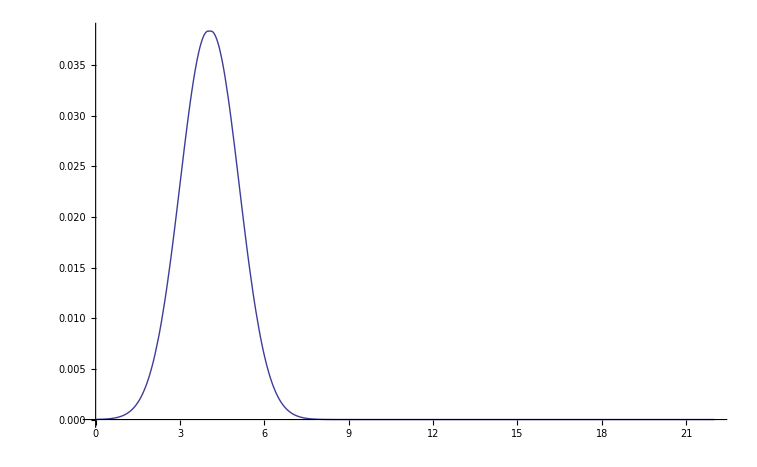

```mathematica
Plot[gaussianPulse[t,0,0.1,1.],{t,0,22,PlotRange->Full]
```

```mathematica
heff = h /. {δ->0.,α->-.240,ϵ->π 0.1 *gaussianPulse[t,10,20,5]};
psisolution = NDSolve[{psi'[t] == -I heff. psi[t],psi[0]=={1,0,0}},psi,{t,0,100}];
```

```mathematica
drive[ϕ_,t_]:= π 0.1 *(gaussianPulse[t,3,5.,1.]+Exp[I ϕ] *gaussianPulse[t,15,5.,1.])
hϕ[t_,ϕ_]:= Block[{δ=-0.16,α=-.240*2,ϵ=drive[ϕ,t]},h /. {δ->δ,α->α,ϵ->ϵ,ϕ->ϕ}] ;
phisolution[ϕ_] := NDSolve[{psi'[t] == -I hϕ[t,ϕ]. psi[t],psi[0]=={1,0,0}},psi,{t,0,30}];
phisequence[ϕ_]:=1-Evaluate[Abs[psi[30.0] /. phisolution[ϕ] ] [[1]]][[1]]^2;
```

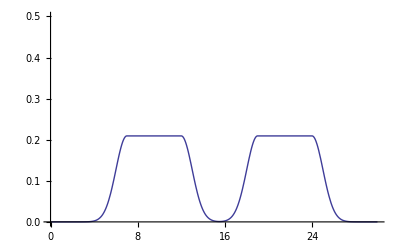

```mathematica
Plot[drive[0,t],{t,0,30},PlotRange->{0,0.5}]
```

```mathematica
phases =Range[0,4π,π/8];
values = Map[phisequence[#]&,phases];
```

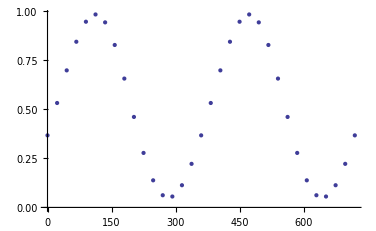

```mathematica
ListPlot[Map[{phases[[#]]*180./π,values[[#]]}&,Range[1,Length[phases]]]]
```

```mathematica
Remove["hrabi"]
hrabi[δ_,α_,ϵ_] := h  /.{δ->δ,α->α,ϵ->ϵ};
hrabi[δ,α,ϵ] //MatrixForm
Remove["rabisolution"]
rabisolution[δ_,α_,ϵ_] := Evaluate[NDSolve[{psi'[t] == -I hrabi[δ,α,ϵ]. psi[t],psi[0]=={1,0,0}},psi,{t,0,100}] /. {δ->δ,α->α,ϵ->ϵ} ]
```

(0 | Conjugate[ϵ]/2 | 0
ϵ/2 | δ | Conjugate[ϵ]/(√2)
0 | ϵ/(√2) | α+2 δ)

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

```mathematica
ds = Range[0.1,1,0.1];
```

```mathematica
gateerrors = Map[Abs[Evaluate[psi[20.] /. (rabisolution[δ,α,ϵ] /. {δ->-0.11*#*π,α->-0.240 2 π,ϵ->#*π  *gaussianPulse[t,0,1.0/#,1.0]})][[1]]] &,ds];
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

General::stop: Further output of NDSolve :: ndnum will be suppressed during this calculation.

```mathematica
gateerrors
```

{{0.0603467,0.996231,0.062304},{0.0519981,0.992613,0.109614},{0.0630933,0.986832,0.148936},{0.0805653,0.987939,0.132232},{0.102785,0.988077,0.114629},{0.128439,0.986271,0.103793},{0.156539,0.982857,0.0974044},{0.186362,0.978077,0.0929193},{0.217365,0.972029,0.0889519},{0.249135,0.964737,0.084933}}

```mathematica
errorslist =MapIndexed[{ds[[#2]][[1]],#1}&,Map[#[[2]]&,gateerrors]];
```

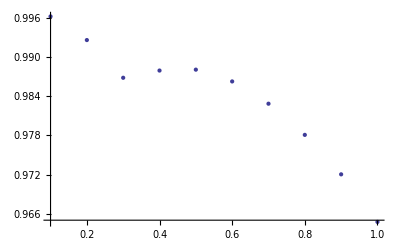

```mathematica
ListPlot[errorslist,PlotRange->Full]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

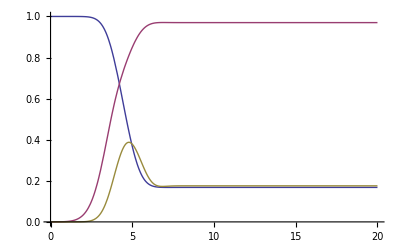

```mathematica
d = 0.1;
ep = 0.2;
myrabisolution = rabisolution[δ,α,ϵ] /. {δ->-0.35,α->-0.240 2 π,ϵ->1./d*π  *gaussianPulse[t,0,d,1.0]};
psit =(Abs[Evaluate[psi[t] /. myrabisolution]])[[1]];
Plot[{psit[[1]],psit[[2]],psit[[3]]},{t,0,20},PlotRange->{0,1}]
```

```mathematica
((psit /.{t->4.248})[[2]]+(psit /.{t->4.248})[[1]])*1./Sqrt[2]
(psit /. {t->10})[[2]]
```

0.947276

0.970048

```mathematica
Evaluate[Release[Hold[rabisolution[δ,α,ϵ] /. {α->-0.240,ϵ->π 0.2 *gaussianPulse[t,0,40,4.]}] /.{δ->0.1,t->1}]]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

{{psi→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
DensityPlot[]
```

DensityPlot::argrx: DensityPlot called with 0 arguments; 3 arguments are expected.

DensityPlot[]

```mathematica
psit.{0,1,0} /.{t->6.18}
```

0.584685

```mathematica
myrabisolution2[δ,α,ϵ]:=rabisolution[δ,α,ϵ]
```

```mathematica
Plot[Abs[myrabisolution2[0.0,α,ϵ] /. {α->-0.240,ϵ->π 0.2 *gaussianPulse[t,0,40,4.]}],{t,0,100}]
```

-Graphics-

```mathematica
Remove["rabistate"]
rabistate[δ_?NumberQ,α_?NumberQ,ϵ_?NumberQ,t_] := Evaluate[psi[t] /. rabisolution[δ,α,ϵ]][[1]]
rabisolution[0.1,-0.24,0]
```

Remove::rmnsm: There are no symbols matching ""rabistate"".

{{psi→InterpolatingFunction[{{0.,100.}},<>]}}

```mathematica
values = Map[Abs[rabistate[0,-0.24,0.1,#]][[1]]&,Range[0,100]];
```

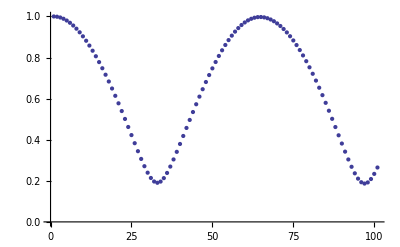

```mathematica
ListPlot[values]
```

```mathematica
'
```

```mathematica
deltas = Range[-0.25,0.25,0.01];
ts = Range[0,100];
values = Map[Block[{δ=#},Map[Abs[rabistate[δ 2 π,-0.24 2 π,0.2π,#]]&,ts]]&,deltas];
```

```mathematica
valuesi[j_]:=Map[Block[{i=#},Map[values[[i]][[#]][[j]]&,Range[1,Length[values[[1]]]]]]&,Range[1,Length[values]]];
```

```mathematica
valueslist = Map[valuesi[#]&,Range[1,3]];
```

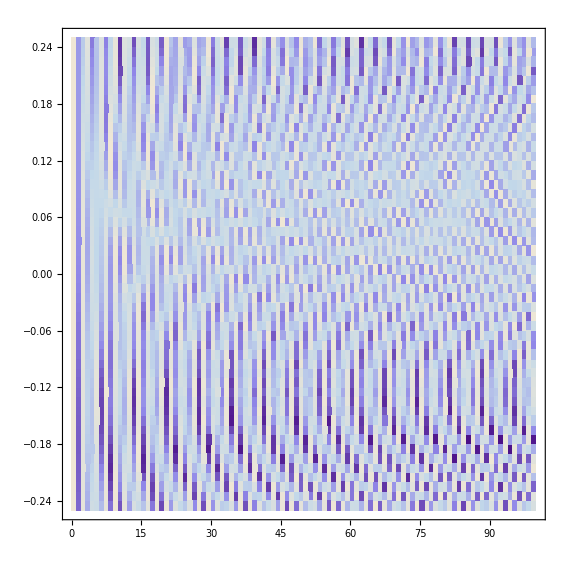
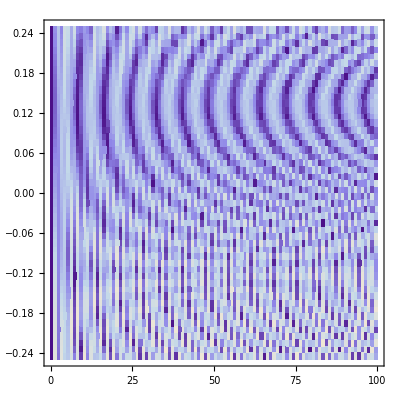
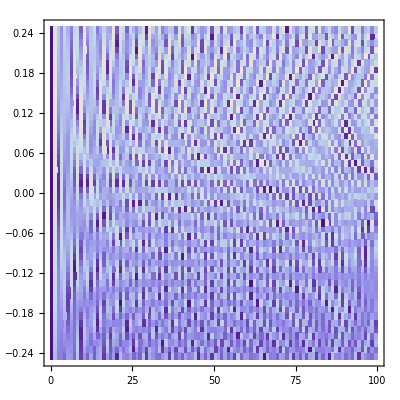

```mathematica
Map[ListDensityPlot[#,DataRange->{{ts[[1]],ts[[-1]]},{deltas[[1]],deltas[[-1]]}},InterpolationOrder->0,PlotRange->{0,1.1}]&,valueslist]
```

```mathematica
hreal = ComplexExpand[h ]
```

{{0,ϵ/2,0},{ϵ/2,δ,ϵ/(√2)},{0,ϵ/(√2),α+2 δ}}

```mathematica
hevs = Eigenvalues[hreal]
hevecs = Eigenvectors[hreal]
```

{Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,1],Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,2],Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,3]}

{{-(α+2 δ-Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,1])/(√2 Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,1]),-(√2 (α+2 δ-Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,1]))/ϵ,1},{-(α+2 δ-Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,2])/(√2 Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,2]),-(√2 (α+2 δ-Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,2]))/ϵ,1},{-(α+2 δ-Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,3])/(√2 Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,3]),-(√2 (α+2 δ-Root[α ϵ^2+2 δ ϵ^2+(4 α δ+8 δ^2-3 ϵ^2) #1+(-4 α-12 δ) #1^2+4 #1^3&,3]))/ϵ,1}}

```mathematica
driveStrengths = Range[0,2.0,1./10.];
minima = Map[FindMinimum[hevs[[3]]-hevs[[2]] /.{α->-0.24 2π,ϵ->#*π},{δ},PrecisionGoal->0.00001]&,driveStrengths];
shifts = Map[#[[2]][[1]][[2]]&,minima];
```

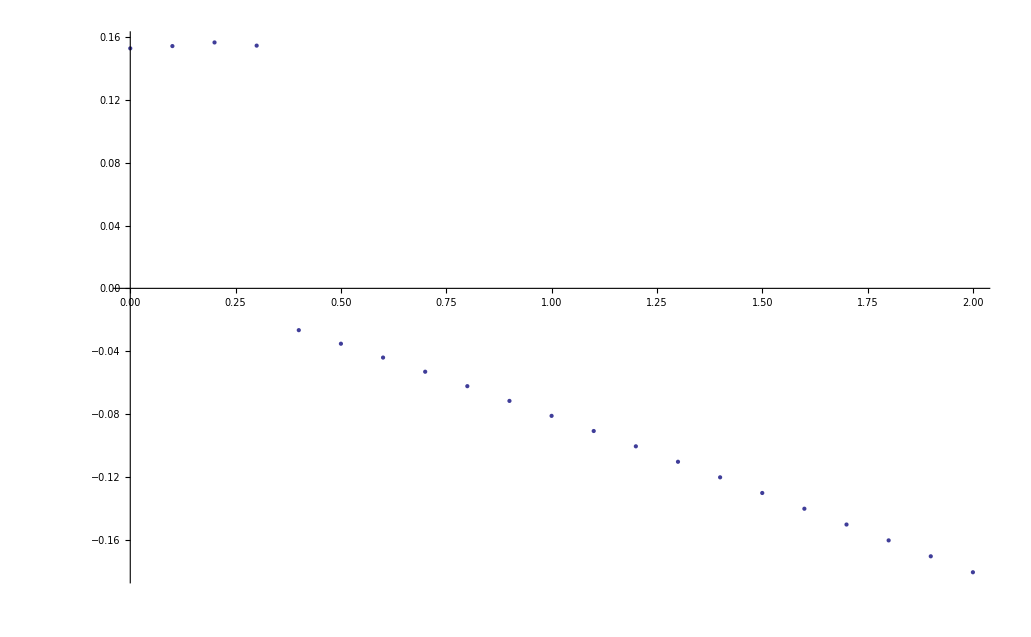

```mathematica
lp = ListPlot[Map[{driveStrengths[[#]],shifts[[#]]/π}&,Range[1,Length[shifts]]]];
Show[lp]
```

```mathematica
4./π/4.
```

0.31831

```mathematica
10./π^2
```

1.01321

```mathematica
evs = Eigenvalues[{{-e/2,ϵ/2},{ϵ/2,e/2}}]
```

{-1/2 √(e^2+ϵ^2),1/2 √(e^2+ϵ^2)}

```mathematica
f01 = ComplexExpand[evs[[2]]-evs[[1]]]
```

√(e^2+ϵ^2)

```mathematica
f01 /. {ϵ->1.0 2 *π,e->0}
```

6.28319

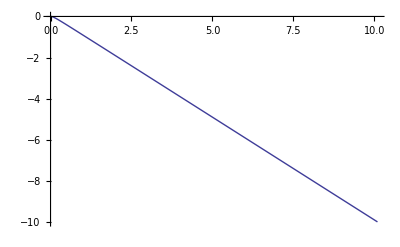

```mathematica
pl =Plot[(-Sqrt[δ^2+(ϵ)^2] +δ)/. {δ->0.1},{ϵ,0,40.0},PlotRange->{{0,10},{0,-10}}]
```

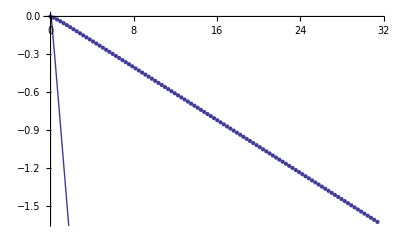

```mathematica
Show[lp,pl]
```

```mathematica
hevs
```

{Root[α ϵ^2+2 π δ ϵ^2+(4 π α δ+8 π^2 δ^2-3 ϵ^2) #1+(-4 α-12 π δ) #1^2+4 #1^3&,1],Root[α ϵ^2+2 π δ ϵ^2+(4 π α δ+8 π^2 δ^2-3 ϵ^2) #1+(-4 α-12 π δ) #1^2+4 #1^3&,2],Root[α ϵ^2+2 π δ ϵ^2+(4 π α δ+8 π^2 δ^2-3 ϵ^2) #1+(-4 α-12 π δ) #1^2+4 #1^3&,3]}

```mathematica
wp = {α->-0.24 2 π,δ->δ,ϵ->ϵ};
hevecswp = hevecs /. wp;
hevecswp = Map[#/Norm[#]&,hevecswp];
hevswp = hevs /. wp;
```

```mathematica
osc= Total[Map[hevecswp[[#]]*hevecswp[[#]][[1]]*Exp[-I hevswp[[#]]t]&,Range[1,Length[hevswp]]]];
```

```mathematica
ep = 0.1π;
Maximize[{Abs[osc[[2]] /. {ϵ->ep}]^2,δ<0,t>0},{t,δ}]
```

{0.978406,{t→9.97364,δ→-0.0304688}}

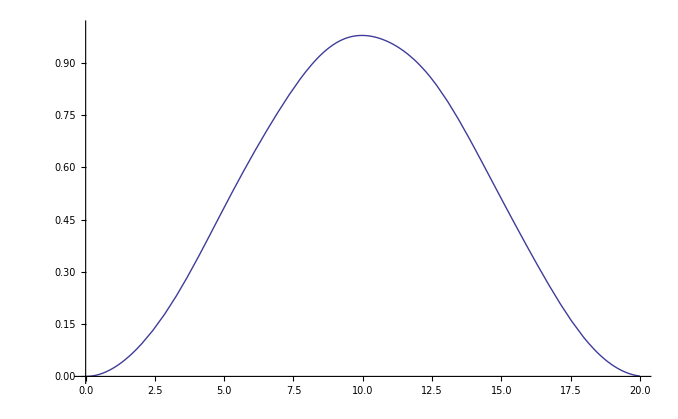

```mathematica
Plot[Abs[osc[[2]]/.{ϵ->ep,δ->-0.0304}]^2 ,{t,0,20},PlotRange->{0,1}]
```

```mathematica
epsilons = Range[0.01π,0.3π,0.0025π];
errors = Map[Maximize[{Abs[osc[[2]] /.{ϵ->#}],δ<0,t>0},{t,δ}]&,epsilons];
```

```mathematica
gateerrors = Map[{epsilons[[#]]/π,errors[[#]][[1]]}&,Range[1,Length[epsilons]]];
gatetimes = Map[{epsilons[[#]]/π,errors[[#]][[2]][[1]][[2]]}&,Range[1,Length[epsilons]]];
detunings = Map[{epsilons[[#]]/π,errors[[#]][[2]][[2]][[2]]}&,Range[1,Length[epsilons]]];
```

```mathematica
Export["E:\\cygwin\\home\\adewes\\thesis\\material\\mathematica\\drive_errors.xls",{gateerrors,gatetimes,detunings},"XLS"]
```

E:\cygwin\home\adewes\thesis\material\mathematica\drive_errors.xls

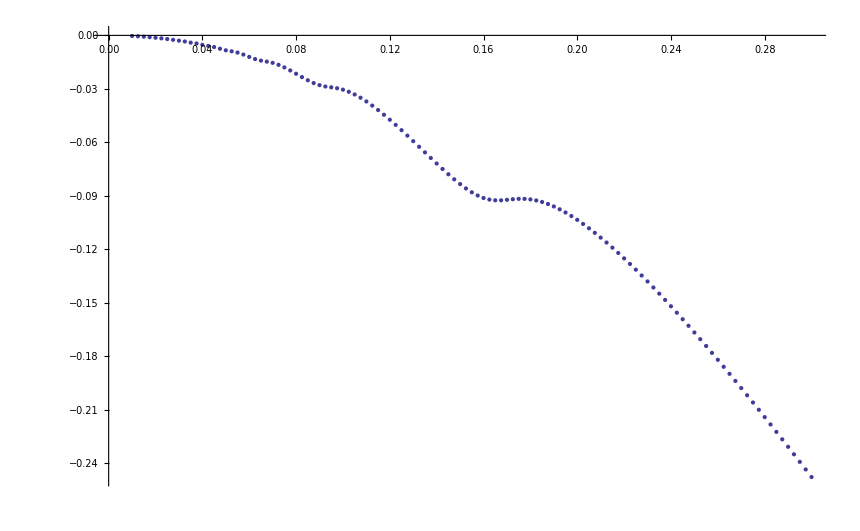

```mathematica
Show[ListPlot[detunings]]
```

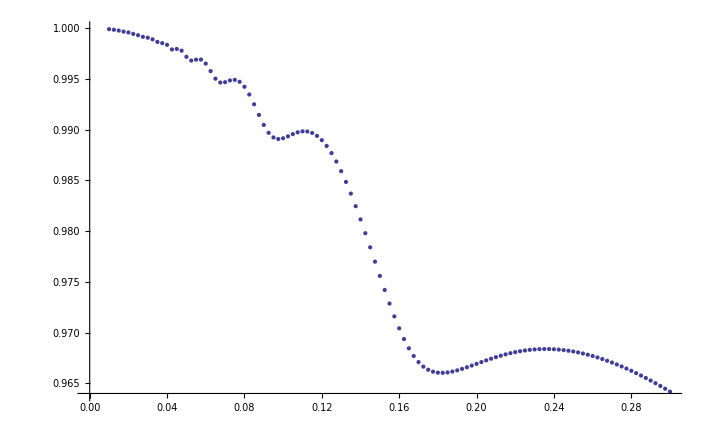

```mathematica
ListPlot[gateerrors]
```

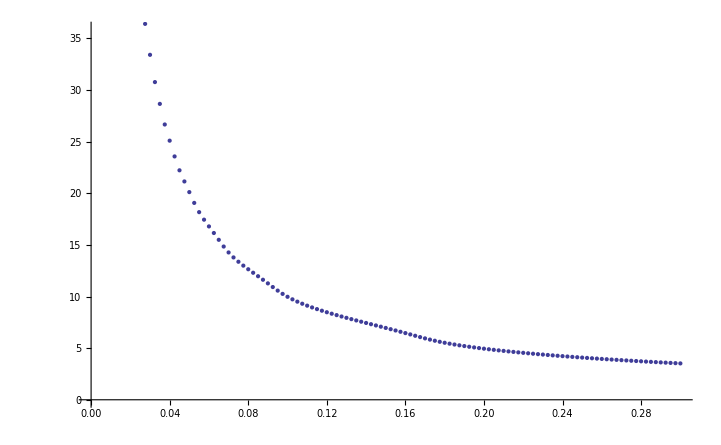

```mathematica
ListPlot[gatetimes]
```

```mathematica
DensityPlot[,{t,0,50},{δ,-0.5 ,0.5},WorkingPrecision->10,PlotPoints->80]
```

$Aborted

```mathematica
gridPoints = Map[Block[{t=#},Map[Block[{δ=#},Abs[osc[[2]] /. {ϵ->0.2π,δ->2π δ}]^2]&,Range[-2.0,2.0,0.025]]]&,Range[0,50,0.25]];
```

```mathematica
ListDensityPlot[gridPoints,InterpolationOrder->1,DataRange->{{-2/2/π,2/2/π},{0,50}}]
```

-Graphics-

```mathematica
Export["E:\\cygwin\\home\\adewes\\thesis\\material\\mathematica\\3_level_driving.xls",gridPoints,"XLS"]
```

E:\cygwin\home\adewes\thesis\material\mathematica\3_level_driving.xls